Data Stock

260

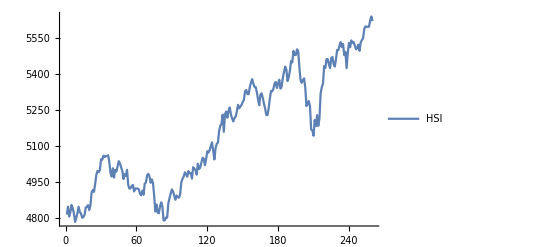

```mathematica
Stock Data

stockData =  FinancialData["^FTSE",{DateObject[{2005,1,1}],DateObject[{2006,1,1}]}];
stockPrices =stockData[[All, 2]];
allRealPrices = stockPrices[[2;;-1]];
allBeforeRealPrices = stockPrices[[1;;-2]];
priceChanges = allRealPrices / allBeforeRealPrices;
Length[stockPrices]
plot = ListLinePlot[{stockPrices},PlotLegends->{"HSI"}]
```

```mathematica
Predictors

sampleSize=40;
windowSize=1;
methods = {"NearestNeighbors", "NeuralNetwork", "RandomForest", "LinearRegression"};
(*methods = {"NeuralNetwork"};*)

predictedPrices = Table[
patterns = Table[priceChanges[[j;;j+windowSize-1]]->priceChanges[[j+windowSize]], {j, i-sampleSize+1,i-windowSize}];
trainingPatterns = patterns[[1;;-2]];
testPatterns = patterns[[-1]];
predictors = Predict[trainingPatterns, Method ->#, PerformanceGoal->"Quality"]&/@  methods;
(*If [i == sampleSize, Print[PredictorInformation[#]] & /@ predictors];*)
#[Keys[testPatterns]]  * allBeforeRealPrices[[i]] & /@  predictors
, {i,sampleSize,Length[priceChanges]}];
realPrices = allRealPrices[[-Length[predictedPrices];;-1]];
beforeRealPrices = allRealPrices[[-Length[predictedPrices]-1;;-2]];
predictedPricesAllMethods = predictedPrices;

AppendTo[methods,"Naive"]
predictedPricesAllMethods = Append[predictedPricesAllMethodsᵀ,beforeRealPrices]ᵀ;
```

Predictors

Predictor results

| MAE | MAPE | Investment profit no fees | Investment profit | Movement accuracy
NearestNeighbors | 2.70729×10^7 | 519226. | 1.13088 | 1.13088 | 0.552273
NeuralNetwork | 2.70801×10^7 | 519347. | 1.13088 | 1.13088 | 0.552273
RandomForest | 2.70808×10^7 | 519358. | 1.13088 | 1.13088 | 0.552273
LinearRegression | 2.71026×10^7 | 519768. | 1.13088 | 1.13088 | 0.552273
Naive | 22.3182 | 0.429048 | 1.13088 | 1.13088 | 0.5

tidilua.tex

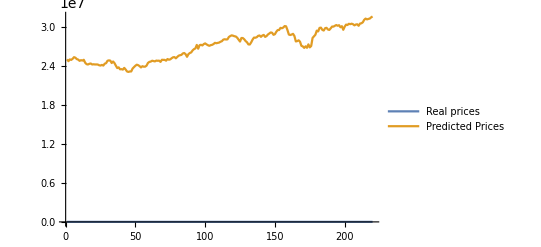

```mathematica
Predictor results

measures = {};
For[i=1, i ≤Length[methods], i++,
predictedPrices = predictedPricesAllMethods[[All,i]];

mae = Total[Abs[ predictedPrices-realPrices]] / Length[realPrices];
mape = Total[Abs[ predictedPrices/realPrices-1]] / Length[realPrices]*100;

movementAccuracy = Total[(Sign[predictedPrices-beforeRealPrices] * Sign[realPrices-beforeRealPrices]+1)/2] / Length[realPrices];

money = 1;
For [t = 2, t ≤Length[predictedPrices], t++,
If [predictedPrices[[t]] ≥realPrices[[t-1]], 
money *= realPrices[[t]] / realPrices[[t-1]];
]
];
moneyNoFees = money;

money = 1;
hasInvested = True;
For [t = 2, t ≤Length[predictedPrices], t++,
transactionFee = money * 0.14 / 100;

If [hasInvested,
If [predictedPrices[[t]] + transactionFee <realPrices[[t-1]],  
money -= transactionFee;
hasInvested=False;
,
money *= realPrices[[t]] / realPrices[[t-1]];
]
,
If [predictedPrices[[t]] - transactionFee ≥realPrices[[t-1]],  
money = (money-transactionFee)*realPrices[[t]] / realPrices[[t-1]];
hasInvested=True;
]
];

]
AppendTo[measures,{mae, mape, moneyNoFees, money, N[movementAccuracy]}]
]


table = TableForm[measures,TableHeadings->{methods, {"MAE", "MAPE", "Investment profit no fees", "Investment profit", "Movement accuracy"}}]
Export["tidilua.tex", table]
ListLinePlot[{realPrices, predictedPricesAllMethods[[All,1]]},PlotLegends->{"Real prices", "Predicted Prices"}]
```

```mathematica
Classifiers

sampleSize = 30;
windowSize =1;
methods = {"NaiveBayes", "LogisticRegression", "NearestNeighbors", "NeuralNetwork", "SupportVectorMachine","RandomForest"};
methods = {"NeuralNetwork"};
priceChanges = allRealPrices;
predictedPrices = ParallelTable[
patterns = Table[priceChanges[[j;;j+windowSize-1]]->Sign[priceChanges[[j+windowSize]]-priceChanges[[j+windowSize-1]]], {j, i-sampleSize+1,i-windowSize}];
trainingPatterns = patterns[[1;;-2]];
testPatterns = patterns[[-1]];
predictors = Classify[trainingPatterns, Method ->#, PerformanceGoal->"TrainingSpeed"]&/@  methods;
(*If [i == sampleSize, Print[ClassifierInformation[#]] & /@ predictors];*)
#[Keys[testPatterns]] & /@  predictors
, {i,sampleSize,Length[priceChanges]}]
realPrices = allRealPrices[[-Length[predictedPrices];;-1]];
beforeRealPrices = allRealPrices[[-Length[predictedPrices]-1;;-2]];
predictedPricesAllMethods = predictedPrices;

AppendTo[methods,"Naive"]
predictedPricesAllMethods = Append[predictedPricesAllMethodsᵀ,beforeRealPrices]ᵀ;
```

Classifiers

LinkObject::linkd: Unable to communicate with closed link LinkObject["'/Applications/Mathematica.app/Contents/MacOS/MathKernel' -subkernel -noinit -mathlink", 1076, 5].

KernelObject::rdead: Subkernel connected through KernelObject[1, "local"] appears dead.

LinkObject::linkd: Unable to communicate with closed link LinkObject["'/Applications/Mathematica.app/Contents/MacOS/MathKernel' -subkernel -noinit -mathlink", 1077, 6].

KernelObject::rdead: Subkernel connected through KernelObject[2, "local"] appears dead.

LinkObject::linkn: Argument LinkObject["'/Applications/Mathematica.app/Contents/MacOS/MathKernel' -subkernel -noinit -mathlink", 1077, 6] in LinkReadyQ[LinkObject["'/Applications/Mathematica.app/Contents/MacOS/MathKernel' -subkernel -noinit -mathlink", 1077, 6]] has an invalid LinkObject number; the link may be closed.

LinkObject::linkn: Argument LinkObject["'/Applications/Mathematica.app/Contents/MacOS/MathKernel' -subkernel -noinit -mathlink", 1077, 6] in LinkRead[LinkObject["'/Applications/Mathematica.app/Contents/MacOS/MathKernel' -subkernel -noinit -mathlink", 1077, 6], Hold] has an invalid LinkObject number; the link may be closed.

KernelObject::rdead: Subkernel connected through KernelObject[2, "local"] appears dead.

General::stop: Further output of KernelObject :: rdead will be suppressed during this calculation.

LinkObject::linkn: Argument LinkObject["'/Applications/Mathematica.app/Contents/MacOS/MathKernel' -subkernel -noinit -mathlink", 1076, 5] in LinkReadyQ[LinkObject["'/Applications/Mathematica.app/Contents/MacOS/MathKernel' -subkernel -noinit -mathlink", 1076, 5]] has an invalid LinkObject number; the link may be closed.

General::stop: Further output of LinkObject :: linkn will be suppressed during this calculation.

LaunchKernels::clone: Kernel KernelObject[2, "local", "<defunct>"] resurrected as KernelObject[3, "local"].

LaunchKernels::clone: Kernel KernelObject[1, "local", "<defunct>"] resurrected as KernelObject[4, "local"].

{{1},{1},{1},{-1},{1},{-1},{-1},{1},{1},{1},{1},{1},{1},{1},{-1},{-1},{-1},{-1},{1},{1},{1},{1},{-1},{1},{-1},{1},{1},{1},{1},{1},{1},{1},{1},{-1},{-1},{-1},{-1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{-1},{1},{-1},{-1},{-1},{1},{-1},{-1},{1},{1},{1},{-1},{-1},{-1},{-1},{-1},{-1},{-1},{-1},{-1},{-1},{-1},{-1},{-1},{-1},{1},{-1},{-1},{1},{1},{-1},{1},{-1},{-1},{-1},{-1},{-1},{-1},{-1},{-1},{-1},{-1},{-1},{-1},{-1},{-1},{1},{1},{1},{-1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{-1},{-1},{1},{1},{1},{1},{1},{1},{1},{1},{-1},{-1},{-1},{-1},{-1},{1},{1},{1},{1},{1},{-1},{1},{1},{1},{1},{1},{-1},{1},{1},{1},{-1},{1},{1},{1},{1},{1},{1},{1},{-1},{-1},{-1},{-1},{-1},{-1},{-1},{-1},{-1},{-1},{1},{-1},{1},{1},{1},{1},{1},{-1},{1},{-1},{1},{1},{-1},{-1},{-1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{-1},{-1},{-1},{-1},{-1},{-1},{-1},{-1},{1},{1},{1},{-1},{-1},{-1},{-1},{-1},{-1},{-1},{1},{1},{-1},{-1},{1},{-1},{-1},{1},{-1},{-1},{-1},{1},{1},{-1},{-1},{-1},{-1},{-1},{-1},{-1},{1},{1},{-1},{1},{-1},{-1},{-1},{1},{1},{1},{1},{0},{0},{1}}

{NeuralNetwork,Naive}

```mathematica
Classifiers results

measures = {};
For[i=1, i ≤Length[methods], i++,
predictedPrices = predictedPricesAllMethods[[All,i]];
movementAccuracy = Total[(predictedPrices * Sign[realPrices-beforeRealPrices]+1)/2] / Length[realPrices];
money = 1;
For [t = 2, t ≤Length[predictedPrices], t++,
If [predictedPrices[[t]] > 0,
money *= realPrices[[t]] / realPrices[[t-1]];
]
];
AppendTo[measures,{N[(money-1),3]*100, N[movementAccuracy,3]*100}]
]


table = TableForm[measures,TableHeadings->{methods, {"Investment profit", "Movement accuracy"}}]

ListPlot
```

| Investment profit | Movement accuracy
NeuralNetwork | -2.03112 | 44.9
Naive | -0.610889 | -7064.94

ListPlot